```mathematica
ClearAll["Global`*"]
```

```mathematica
Off[Solve::svars];
Off[Solve::ratnz];
Off[Inverse::luc];
```

```mathematica
error=500;
choperror=10^-50;
```

```mathematica
dim=242;
```

### Define functions

```mathematica
Tetrahedra=Subsets[{1,2,3,4,5},{4}];
```

```mathematica
edgeor=Subsets[#,{2}]&/@Tetrahedra;
```

```mathematica
facor=Subsets[#,{3}]&/@Tetrahedra;
```

```mathematica
etof={{1,2},{1,3},{2,3},{4,5}};
```

```mathematica
η=DiagonalMatrix[{-1,1,1,1}];
```

```mathematica
sigmabar4=Join[{IdentityMatrix[2]},-Table[PauliMatrix[i],{i,1,3}]];
```

```mathematica
Jvec={{{0,1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0},{1,0,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,0}},-{{0,0,0,0},{0,0,0,0},{0,0,0,-1},{0,0,1,0}},-{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,-1,0,0}},{{0,0,0,0},{0,0,1,0},{0,-1,0,0},{0,0,0,0}}};
```

```mathematica
jjvec=Join[1/2Table[PauliMatrix[i],{i,1,3}],I/2Table[PauliMatrix[i],{i,1,3}]];
```

```mathematica
normso13[n_,m_]:=n.η.m
```

```mathematica
Tetnormal[bdypoints_,n_]:=Block[{edgevec,a,b,c,d,eqs,soleqs,normalize,normsoleqs},edgevec=bdypoints⟦#⟦1⟧⟧-bdypoints⟦#⟦2⟧⟧&/@(edgeor⟦n⟧);
eqs=Thread[({a,b,c,d}.η.# & /@ edgevec[[1;;4]])==0];
soleqs=Solve[eqs,{a,b,c,d}][[1]];
normalize={a,b,c,d}/Sqrt[Abs[normso13[{a,b,c,d},{a,b,c,d}]]];
normsoleqs=FullSimplify[normalize/.soleqs,Join[{a>0,b>0,c>0,d>0},Thread[{a,b,c,d}ϵ Reals]]];
If[normso13[normsoleqs,normsoleqs]<0,If[normsoleqs[[1]]>0,normsoleqs,-normsoleqs],Print["It's timelike Tetrahedron"]]
]
```

```mathematica
vectospinor[aa_]:={{aa[[1]]+aa[[4]],aa[[2]]-I aa[[3]]},{aa[[2]]+I aa[[3]],aa[[1]]-aa[[4]]}}
```

```mathematica
getreim[ff_,assume_]:=Simplify[({Re[#],Im[#]}& @ ff //ExpandAll//FunctionExpand),Assumptions->assume]
```

```mathematica
getsl2c[n1_,n2_]:=Block[{sn2=vectospinor[n2],
sn1=vectospinor[n1],ggi,soleqggisn,ggire,a1,a2,b1,b2,c1,c2,d1,d2,eqggisn,symbolsoleqggisn,symbolinstancesoleqggisn},
ggi=FullSimplify[{{a1+I a2 ,b1+I b2},{c1+ I c2,d1+ I d2}}.sn1.ConjugateTranspose[{{a1+I a2 ,b1+I b2},{c1+ I c2,d1+ I d2}}],{a1,a2,b1,b2,c1,c2,d1,d2}∈ Reals];eqggisn=DeleteCases[Thread[(getreim[ggi,{a1,a2,b1,b2,c1,c2,d1,d2}∈ Reals]-getreim[sn2,{a1,a2,b1,b2,c1,c2,d1,d2}∈ Reals]//Flatten)==0],True];
soleqggisn=Solve[Join[eqggisn,{Det[{{a1+I a2 ,b1+I b2},{c1+ I c2,d1+ I d2}}]==1}],{a1,a2,b1,b2,c1,c2,d1,d2}][[1]];symbolsoleqggisn= DeleteDuplicates@Cases[{a1,a2,b1,b2,c1,c2,d1,d2}/.soleqggisn,_Symbol,-1];symbolinstancesoleqggisn=FindInstance[Thread[DeleteDuplicates@Cases[soleqggisn,Sqrt[xx$111_]->xx$111,-1]>0],symbolsoleqggisn,Reals][[1]];ggire={{a1+I a2 ,b1+I b2},{c1+ I c2,d1+ I d2}}/.soleqggisn/.symbolinstancesoleqggisn]
```

```mathematica
getsl2c[nn_]:=getsl2c[{1,0,0,0},nn]
```

```mathematica
getso13[sl2cg_]:=Table[1/2Tr[sl2cg.sigmabar4⟦i⟧.ConjugateTranspose[sl2cg].sigmabar4⟦j⟧],{i,1,4},{j,1,4}]
```

```mathematica
getarea[vert1_,vert2_,vert3_]:=Block[{len1,len2,len3,area,edgevec1,edgevec2,edgevec3},edgevec1=vert1-vert2;
edgevec2=vert1-vert3;
edgevec3=vert2-vert3;
len1=Sqrt[Abs[normso13[edgevec1,edgevec1]]];len2=Sqrt[Abs[normso13[edgevec2,edgevec2]]];len3=Sqrt[Abs[normso13[edgevec3,edgevec3]]];
area=Sqrt[(len1+len2+len3)/2((len1+len2+len3)/2-len1)((len1+len2+len3)/2-len2)((len1+len2+len3)/2-len3)]]
```

```mathematica
get3dtet[tetlenthvec_,tetsol13_]:=Block[{tet3dvec$111},tet3dvec$111=(tetsol13.#)&/@tetlenthvec;
If[(#⟦1⟧//N//Chop)==0,Drop[#,1],Print["It's not a good SO(1,3)"]]&/@ tet3dvec$111
]
```

```mathematica
getfacevec[tetedgevec_]:=Cross[tetedgevec[[#[[1]]]],tetedgevec[[#[[2]]]]]& /@ etof
```

```mathematica
getoutpfacevec[tetedgevec_]:=Block[{rrr$111=getfacevec[tetedgevec],nvec$111,meta$111},nvec$111=rrr$111;meta$111=DiagonalMatrix[{1,1,1}];(Sign/@(Table[{tetedgevec[[3]],tetedgevec[[2]],tetedgevec[[1]],-tetedgevec[[1]]}[[i]].meta$111.nvec$111[[i]],{i,Length[nvec$111]}])) nvec$111]
```

```mathematica
getfacenormal[facevec_]:= Block[{meta=DiagonalMatrix[{1,1,1}]},#/Sqrt[Abs[(#.meta.# )]]&/@ facevec]
```

```mathematica
getbivec[n1_,n2_]:=1/2Table[Sum[LeviCivitaTensor[4][[i,j,k,l]](η.n1)[[k]](η.n2)[[l]],{k,1,4},{l,1,4}],{i,1,4},{j,1,4}].η
```

```mathematica
threetofour[n_]:=Join[{0},n]
```

```mathematica
bivec1tohalf[bivec_]:=Total[ 1/2 Join[Table[Tr[bivec.Jvec[[i]]],{i,1,3}],-Table[Tr[bivec.Jvec[[i]]],{i,4,6}]]*jjvec]
```

```mathematica
eqssu2=DeleteCases[DeleteDuplicates[Thread[(FullSimplify[{Re[#],Im[#]}& /@ ExpandAll[Join[Flatten[(({{a$eqt,b$eqt},{-Conjugate[b$eqt],Conjugate[a$eqt]}}.PauliMatrix[3].Inverse[{{a$eqt,b$eqt},{-Conjugate[b$eqt],Conjugate[a$eqt]}}]-Total[{ee$eqt,ff$eqt,gg$eqt}*Table[PauliMatrix[i],{i,1,3}]]/.a$eqt Conjugate[a$eqt]+b$eqt Conjugate[b$eqt]->1))],{a$eqt Conjugate[a$eqt]+b$eqt Conjugate[b$eqt]-1}]/.a$eqt->aa1$eqt+I aa2$eqt/.b$eqt->bb1$eqt+I bb2$eqt],{aa1$eqt,aa2$eqt,bb1$eqt,bb2$eqt,ee$eqt,ff$eqt,gg$eqt}∈ Reals]//Flatten)==0]//FullSimplify],True];

soleqssu2$eqs=(Solve[eqssu2[[1;;3]],{aa1$eqt,aa2$eqt,bb1$eqt,bb2$eqt}]/.ee$eqt^2+ff$eqt^2+gg$eqt^2->1//FullSimplify)//.ff$eqt^2->1-ee$eqt^2-gg$eqt^2//FullSimplify;

soleqssu2=soleqssu2$eqs[[Position[Total[Transpose@Boole[(eqssu2/.soleqssu2$eqs//.ff$eqt^2->1-ee$eqt^2-gg$eqt^2//FullSimplify)//.ff$eqt^2->1-ee$eqt^2-gg$eqt^2//FullSimplify],1],Length[eqssu2]][[1,1]]]];

soleqssu2$aa1=Solve[Cases[soleqssu2[[1]],Sqrt[xx$eqt_]->xx$eqt,-1]==0,aa1$eqt][[-1]];

soleqssu2ta=If[(aa1$eqt/.soleqssu2$aa1) ∈ Reals,Evaluate[Join[soleqssu2$aa1,soleqssu2/.soleqssu2$aa1]],Evaluate[Join[{aa1$eqt->0},soleqssu2/.aa1$eqt->0]]];

getsu2frombivec[bivec_]:={{aa1$eqt+ⅈ aa2$eqt,bb1$eqt+ⅈ bb2$eqt},{-bb1$eqt+ⅈ bb2$eqt,aa1$eqt-ⅈ aa2$eqt}}/.(soleqssu2ta/.Thread[{ee$eqt,ff$eqt,gg$eqt} ->Re[Tr[bivec.#]& /@ Table[PauliMatrix[i],{i,1,3}] ]])
```

```mathematica
getxifromsu2[hsu_]:=Transpose[hsu.{{1},{0}}]//Flatten
```

```mathematica
bivecdual[bivec_]:=HodgeDual[η.bivec].η
```

```mathematica
getz[gsl2c_,bdxi_]:=Inverse[ConjugateTranspose[gsl2c]].bdxi/(Inverse[ConjugateTranspose[gsl2c]].bdxi)[[1]]
```

```mathematica
gettetoutnormalvec[bdypoint_,n_]:=Block[{coordinates,l1,l2,l3,nn,norm,FScenter},
coordinates=bdypoint⟦#⟧&/@Tetrahedra⟦n⟧;
{l1,l2,l3}=(coordinates⟦#⟦1⟧⟧-coordinates⟦#⟦2⟧⟧)&/@{{1,2},{1,3},{1,4}}; nn=LeviCivitaTensor[4].(η.l1).(η.l2).(η.l3); norm = Sqrt[-nn.η.nn] ;
FScenter=Total[bdypoint]/Length[bdypoint];
If[Refine[nn.(η.(coordinates⟦1⟧-FScenter))>0],Return[nn/norm],Return[-nn/norm]];
]
```

```mathematica
dihedralAngle[bdypoints_,a_,b_]:=Block[{TetNormalsN,TetNormalsM,sign},
TetNormalsN=gettetoutnormalvec[bdypoints,a];
TetNormalsM=gettetoutnormalvec[bdypoints,b];
sign=If[Sign[TetNormalsN⟦1⟧]==Sign[TetNormalsM⟦1⟧],-1,1];
sign*Re[ArcCosh[TetNormalsN.η.TetNormalsM]]
]
```

### solution function

```mathematica
getsolution[bdypoints_]:=Block[{ll$111=Length[bdypoints],edgevec,tetnormalvec,solgsl2c,solgso13,areaef,areaef55,threedtetfacenormal,threededgevec,threeto4dedgevec,bdybivec,bdybivec55,bdybivec55s,bdysu,bdyxin,threeto4dtetfacenormal,bdybivecsign,bdybivecsignn,bdybivecsignn55,bdybivecsignn55dual,bdybivecsignn55sd,aainter$121,fullkappa,re$111,threedtetfacenormal55,xv,bdyz},edgevec=Table[(bdypoints⟦#⟦1⟧⟧-bdypoints⟦#⟦2⟧⟧)& /@edgeor⟦j⟧,{j,1,ll$111}];tetnormalvec=Table[Tetnormal[bdypoints,j],{j,1,ll$111}];
solgsl2c=Table[getsl2c[tetnormalvec⟦i⟧],{i,1,ll$111}];
solgso13=Table[getso13[solgsl2c⟦i⟧],{i,1,ll$111}];
areaef=Table[getarea[bdypoints⟦#⟦1⟧⟧,bdypoints⟦#⟦2⟧⟧,bdypoints⟦#⟦3⟧⟧]&/@facor⟦i⟧,{i,1,ll$111}];
areaef55=Table[Insert[areaef[[i]],0,i],{i,1,5}];

threededgevec=Table[get3dtet[edgevec[[i]],solgso13[[i]]],{i,1,ll$111}];
threedtetfacenormal=Table[getfacenormal@getoutpfacevec[threededgevec⟦i⟧],{i,ll$111}];
threedtetfacenormal55=Table[Insert[threedtetfacenormal[[i]],{0,0,0},i],{i,1,5}];

threeto4dedgevec = Table[threetofour[#]& /@ threededgevec[[i]],{i,1,ll$111}];
threeto4dtetfacenormal=Table[threetofour[#]& /@ threedtetfacenormal[[i]],{i,1,ll$111}];

bdybivec=Table[getbivec[threeto4dedgevec [[i,#[[1]]]],threeto4dedgevec [[i,#[[2]]]]]&/@ etof,{i,1,ll$111}];
bdybivec55=Table[Insert[#/Sqrt[Abs[1/2Tr[#.#]]]& /@ bdybivec[[i]],Jvec[[3]],i],{i,1,5}];
bdybivec55s=Table[bivec1tohalf[#] & /@ (bdybivec55[[i]]//Normal),{i,1,ll$111}];
bdysu=Table[getsu2frombivec[bdybivec55s[[i,j]]],{i,1,ll$111},{j,1,ll$111}];bdyxin=Table[getxifromsu2[bdysu[[i,j]]],{i,1,ll$111},{j,1,ll$111}];

bdybivecsign=Table[getbivec[{1,0,0,0},#]&/@ threeto4dtetfacenormal[[i]],{i,1,ll$111}];bdybivecsignn=Table[#/(Sqrt[1/2Abs[Tr[#.#]]])&/@ bdybivecsign[[i]],{i,1,ll$111}];
bdybivecsignn55=Table[Insert[bdybivecsignn[[i]],Jvec[[3]],i],{i,1,ll$111}];
bdybivecsignn55dual=Table[bivecdual[#] & /@ bdybivecsignn55[[i]],{i,1,ll$111}];
bdybivecsignn55sd=Table[bivec1tohalf[#] & /@ (bdybivecsignn55dual[[i]]//Normal),{i,1,ll$111}];fullkappa=Join[{#[[1]]},Table[-#[[i]]/#[[i,1]]/#[[1,i]],{i,2,ll$111}] ]& @((Total[(bdybivec55s),{3,4}]/(Total[(bdybivecsignn55sd),{3,4}]/. 0->aainter$121)//Chop//Round));

re$111={fullkappa,areaef55,threedtetfacenormal55,solgsl2c,bdyxin,bdybivec55s}

]
```

### setup coordinates and index at Curve geometry

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"vertex7Coor.wl"}]];
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Orientation.wl"}]];
```

```mathematica
FourSimplices=Flatten[Table[Join[#,{i}]&/@(Join[{1,2},#]&/@Subsets[{3,4,5},{2}]),{i,6,7}],1];
```

### curved geometry to find P6

```mathematica
distance[V_,i_,j_]:=Block[{ge},ge=DiagonalMatrix[{-1,1,1,1}];(V⟦i⟧-V⟦j⟧).ge.(V⟦i⟧-V⟦j⟧)]
```

```mathematica
VertexToGet5[vert_,ls35_]:=Block[{v5,t5,x5,y5,z5,eqns1,eqns2,Vertex1To7,Vertex17,eqns,sols},
v5={t5,x5,y5,z5};
Vertex1To7=Array[0&,{7,4}];
Table[Vertex1To7[[FourSimplices[[vert,i]]]]=Vertex7[[FourSimplices[[vert,i]]]],{i,5}];
Vertex17=Join[Vertex1To7[[1;;4]],{v5},Vertex1To7[[6;;7]]];
If[vert==2||vert==5,eqns=Table[distance[Vertex17,5,FourSimplices[[vert,i]]]==ls35[[5,FourSimplices[[vert,i]]]],{i,{1,2,3,5}}];
(Vertex17/.Solve[eqns,{t5,x5,y5,z5}][[1]])[[#]]&/@FourSimplices[[vert]],Vertex7[[#]]&/@FourSimplices[[vert]]]
]
```

```mathematica
Vertex7NewCoor[ls35_]:=Block[{comple,insert1},Table[comple=Complement[{1,2,3,4,5,6,7},FourSimplices[[i]]];insert1=Insert[VertexToGet5[i,ls35],{0,0,0,0},comple[[1]]];Insert[insert1,{0,0,0,0},comple[[2]]],{i,6}]];
```

```mathematica
BDdataInitial[ls35_]:=Block[{gv,xv,zv,sol1,sol2,sol3,sol4,sol5,sol6,bdypoints1,bdypoints2,bdypoints3,bdypoints4,bdypoints5,bdypoints6,kappa,Arv,nabi,gvi,xvi,zvi,bivec,pp,su2,gvn0,sl2c,gv1,xv1,gaugesu2},

{bdypoints1,bdypoints2,bdypoints3,bdypoints4,bdypoints5,bdypoints6}=Table[VertexToGet5[i,ls35],{i,6}];

sol1=getsolution[bdypoints1];
sol2=getsolution[bdypoints2];
sol3=getsolution[bdypoints3];
sol4=getsolution[bdypoints4];
sol5=getsolution[bdypoints5];
sol6=getsolution[bdypoints6];

{kappa,Arv,nabi,gvi,xvi,bivec}=Thread[{sol1,sol2,sol3,sol4,sol5,sol6}];

{Arv,nabi,xvi}

]
```

### Gauge fixing

```mathematica
connectionref={{1,1},{1,2},{1,3},{2,1},{2,3},{3,1},{4,2},{4,3},{5,3}};
connectionchange={{4,1},{2,2},{3,2},{5,1},{3,3},{6,1},{5,2},{6,2},{6,3}};
```

```mathematica
SO3[nabchange_,nabref_]:=Block[{matrixso3,eqns,variables,sol},matrixso3=Table[ToExpression["a"<>ToString[i]<>ToString[j]],{i,1,3},{j,1,3}];
eqns=Thread[matrixso3.#&/@nabchange-nabref]//Flatten;
variables=Flatten[matrixso3];
sol=Solve[DeleteCases[Thread[eqns==0],True][[1;;11]],variables][[1]];
If[Sequence@@DeleteDuplicates[Chop[eqns/.sol,choperror]]==0&&Det[matrixso3/.sol]==1,matrixso3/.sol,"WrongSO3"]
]
```

```mathematica
SO3ToSU2[so3_]:=Block[{el,su2},el=EulerAngles[so3];
su2=Table[WignerD[{1/2,m1,m2},el[[1]],el[[2]],el[[3]]],{m1,-1/2,1/2},{m2,-1/2,1/2}]]
```

```mathematica
hsu2[n_,nab_,xvi_]:=Block[{refpos,m,refnab,refxvi,changexvi,changenab,su2,so3,change,compare},

refpos=Position[connectionchange,n][[1,1]];
m=connectionref⟦refpos⟧;

refnab=DeleteCases[nab[[Sequence@@m]],nab[[Sequence@@m,m⟦2⟧]]];
refxvi=DeleteCases[xvi[[Sequence@@m]],xvi[[Sequence@@m,m⟦2⟧]]];
changenab=DeleteCases[nab[[Sequence@@n]],nab[[Sequence@@n,n⟦2⟧]]];
changexvi=DeleteCases[xvi[[Sequence@@n]],xvi[[Sequence@@n,n⟦2⟧]]];

so3=SO3[changenab,refnab];
su2=Chop[SO3ToSU2[so3],choperror];

change=su2.#&/@changexvi;
compare=Thread[change/refxvi];
If[Sequence@@DeleteDuplicates[Table[Chop[Abs[compare[[1,i]]-compare[[2,i]]],choperror],{i,Length[compare[[1]]]}]]==0,su2,"WrongSU2"]
]
```

```mathematica
bdFixXi={{1,4},{2,4},{3,4},{4,4},{5,4},{6,4}};
```

```mathematica
bdsu2[n_,nab0_,xv0_,nab_,xv_]:=Block[{refnab,refxvi,changexvi,changenab,su2,so3,change,compare},

refnab=DeleteCases[nab0[[Sequence@@n]],nab0[[Sequence@@n,n⟦2⟧]]];
refxvi=DeleteCases[xv0[[Sequence@@n]],xv0[[Sequence@@n,n⟦2⟧]]];
changenab=DeleteCases[nab[[Sequence@@n]],nab[[Sequence@@n,n⟦2⟧]]];
changexvi=DeleteCases[xv[[Sequence@@n]],xv[[Sequence@@n,n⟦2⟧]]];

so3=SO3[changenab,refnab];
su2=Chop[SO3ToSU2[so3],choperror];

change=su2.#&/@changexvi;
compare=Thread[change/refxvi];
If[Sequence@@DeleteDuplicates[Table[Chop[Abs[compare[[1,i]]-compare[[2,i]]],choperror],{i,Length[compare[[1]]]}]]==0,su2,"WrongSU2"]
]
```

```mathematica
Sl2cToSu2[{{a_,c_},{b_,d_}}]:=Block[{λ,u,v,mu,upper,su2},λ=Sqrt[Abs[b]^2+Abs[d]^2];u=b/λ;v=d/λ;
mu=a*Conjugate[u]+c*Conjugate[v];
upper={{λ^-1,mu},{0,λ}};
su2={{Conjugate[v],-Conjugate[u]},{u,v}};
{upper,su2}]
```

```mathematica
gaugesl2c={{1,2},{2,3},{3,2},{4,2},{5,3},{6,2},{1,1},{2,1},{3,1}};
gaugesl2copp={{2,2},{3,3},{1,3},{5,2},{6,3},{4,3},{4,1},{5,1},{6,1}};
gaugefix=Join[gaugesl2c,gaugesl2copp];
```

```mathematica
GaugeGroup[n_,gv1_]:=Block[{gvn0,sl2c,ksu2,gv2,pp},

If[MemberQ[gaugesl2c,n],gvn0=gv1⟦Sequence@@n⟧;sl2c=Sl2cToSu2[gvn0];ksu2=sl2c[[2]],
pp=Position[gaugesl2copp,n][[1,1]];gvn0=gv1⟦Sequence@@gaugesl2c⟦pp⟧⟧;sl2c=Sl2cToSu2[gvn0];
ksu2=sl2c[[2]]]
]
```

### Curved geometry to find P1

```mathematica
Vertex[vert_,ls35_,ls12_]:=Block[{v1,t1,x1,y1,z1,Vertex7new,Vertex17,eqns,sols},
v1={t1,x1,y1,z1};
Vertex7new=Vertex7NewCoor[ls35];
Vertex17=Join[{v1},Vertex7new[[vert,2;;7]]];
eqns=Table[distance[Vertex17,1,FourSimplices[[vert,i]]]==ls12[[1,FourSimplices[[vert,i]]]],{i,2,5}];
sols=Solve[eqns,{t1,x1,y1,z1},WorkingPrecision->error];
If[vert==3||vert==6,Vertex17/.sols[[2]],Vertex17/.sols[[1]]][[#]]&/@FourSimplices[[vert]]
]
```

```mathematica
BDdata[ls35_,ls12_]:=Block[{gv,xv,zv,sol1,sol2,sol3,sol4,sol5,sol6,bdypoints1,bdypoints2,bdypoints3,bdypoints4,bdypoints5,bdypoints6,kappa,Arv,nabi,gvi,xvi,zvi,bivec,pp,su2,gvn0,sl2c,gv1,xv1,phi,gaugesu2,Av0,nab0,xv0},

{bdypoints1,bdypoints2,bdypoints3,bdypoints4,bdypoints5,bdypoints6}=Table[Chop[Vertex[vert,ls35,ls12],choperror],{vert,Length[FourSimplices]}];

sol1=getsolution[bdypoints1];
sol2=getsolution[bdypoints2];
sol3=getsolution[bdypoints3];
sol4=getsolution[bdypoints4];
sol5=getsolution[bdypoints5];
sol6=getsolution[bdypoints6];

{kappa,Arv,nabi,gvi,xvi,bivec}=Thread[{sol1,sol2,sol3,sol4,sol5,sol6}];

{Av0,nab0,xv0}=BDdataInitial[ls35];

su2=Table[Which[MemberQ[connectionchange,{i,j}],hsu2[{i,j},nabi,xvi],MemberQ[bdFixXi,{i,j}],bdsu2[{i,j},nab0,xv0,nabi,xvi],True,IdentityMatrix[2]],{i,Length[gvi]},{j,Length[gvi⟦i⟧]}];

gv1=Chop[Table[gvi⟦i,j⟧.Inverse[su2⟦i,j⟧],{i,Length[gvi]},{j,Length[gvi⟦i⟧]}],choperror];
xv1=Chop[Table[su2[[i,j]].xvi[[i,j,k]],{i,6},{j,5},{k,5}],choperror];

phi=Table[If[MemberQ[bdFixXi,{i,j}],If[j==k,1,(xv1[[i,j,k]]/xv0[[i,j,k]])[[1]]],1],{i,6},{j,5},{k,5}];

gaugesu2=Table[If[MemberQ[gaugefix,{i,j}],GaugeGroup[{i,j},gv1],IdentityMatrix[2]],{i,Length[gvi]},{j,Length[gvi⟦i⟧]}];

gv=Chop[Table[gv1⟦i,j⟧.Inverse[gaugesu2⟦i,j⟧],{i,Length[gvi]},{j,Length[gvi⟦i⟧]}],choperror];
xv=Chop[Table[gaugesu2[[i,j]].xv1[[i,j,k]]/phi[[i,j,k]],{i,6},{j,5},{k,5}],choperror];

zv=Array[{}&,{6,5,5}];Do[zv⟦Sequence@@EE60⟦i⟧⟧=getz[gv⟦Sequence@@EE60⟦i,1;;2⟧⟧,xv⟦Sequence@@EE60⟦i⟧⟧],{i,Length[EE60]}];

{Arv,gv,xv,zv}

]
```

```mathematica
dihedrals[Arv_,ls35_,ls12_]:=Block[{bdypoints,dihedrals,list,deficit},bdypoints=Table[Vertex[vert,ls35,ls12],{vert,Length[FourSimplices]}];dihedrals=Sum[Sum[Arv⟦i,a,b⟧*dihedralAngle[bdypoints⟦i⟧,a,b],{a,5},{b,a+1,5}],{i,Length[FourSimplices]}];deficit=Table[list=orderInternal⟦i⟧;dihedralAngle[bdypoints⟦list⟦1,1⟧⟧,list⟦1,2⟧,list⟦1,3⟧]+dihedralAngle[bdypoints⟦list⟦3,1⟧⟧,list⟦3,2⟧,list⟦3,3⟧]+dihedralAngle[bdypoints⟦list⟦5,1⟧⟧,list⟦5,2⟧,list⟦5,3⟧]+If[Length[list]==6,0,dihedralAngle[bdypoints⟦list⟦7,1⟧⟧,list⟦7,2⟧,list⟦7,3⟧]],{i,Length[orderInternal]}];
{dihedrals,deficit}]
```

### Action

```mathematica
ExpM[z_List]:=Block[{z1,z2,z3,out},If[Length[z]==6,
z1=1+(z⟦1⟧+I z⟦2⟧)/Sqrt[2];z2=(z⟦3⟧+I z⟦4⟧)/Sqrt[2];z3=(z⟦5⟧+I z⟦6⟧)/Sqrt[2];out={{z1,z2},{z3,(1+z2 z3)/z1}},
z1=1+z⟦1⟧/Sqrt[2];z2=(z⟦2⟧+I z⟦3⟧)/Sqrt[2];z3=z3=1/(1+z⟦1⟧/Sqrt[2]);out={{z1,z2},{0,z3}}]
]
```

```mathematica
ExpMconj[z_List]:=Block[{z1,z2,z3,out},If[Length[z]==6,z1=1+(z⟦1⟧-I z⟦2⟧)/Sqrt[2];z2=(z⟦3⟧-I z⟦4⟧)/Sqrt[2];z3=(z⟦5⟧-I z⟦6⟧)/Sqrt[2];out={{z1,z2},{z3,(1+z2 z3)/z1}},
z1=1+z⟦1⟧/Sqrt[2];z2=(z⟦2⟧-I z⟦3⟧)/Sqrt[2];z3=1/(1+z⟦1⟧/Sqrt[2]);out={{z1,z2},{0,z3}}]]
```

```mathematica
LogM[z_]:=Log[z]
```

```mathematica
Febhalf1[{Arv_,gv_,xv_,zv_},v_,e_,b_,{zvex_,zvey_},gve_List,γ_]:=Block[{gv2e3conj,zv2b,Zv1e2bRight,Xie3bZv2e3b,gv2e3,zv2bconj,Zv2e3bLeft,Zv2e3Zv2e3,areas,output},
gv2e3conj=Transpose[ExpMconj[gve]].ConjugateTranspose[gv⟦v,e⟧];
zv2b={{1},{zv⟦v,e,b⟧[[2]]+zvex+I*zvey}};
Zv1e2bRight=gv2e3conj.zv2b;
Xie3bZv2e3b=Conjugate[xv⟦v,e,b⟧].Zv1e2bRight;

gv2e3=gv⟦v,e⟧.ExpM[gve];
zv2bconj={{1},{Conjugate[zv⟦v,e,b⟧[[2]]]+zvex-I*zvey}};
Zv2e3bLeft=(Transpose[zv2bconj].gv2e3);
Zv2e3Zv2e3=Zv2e3bLeft.Zv1e2bRight;

areas=Arv⟦v,e,b⟧/γ;

output=Flatten[areas*(2*LogM[Xie3bZv2e3b]-LogM[Zv2e3Zv2e3])-I *γ*areas*LogM[Zv2e3Zv2e3]]⟦1⟧
]
```

```mathematica
Febhalf2[{Arv_,gv_,xv_,zv_},v_,e1_,e2_,ve1f_,ve2f_,{zve1fx_,zve1fy_},gve2_List,γ_]:=Block[{gv1e2,zv1bconj,Zv1e2bLeft,Zv1e2bXie2b,gv1e2conj,zv1b,Zv1e2bRight,ZveZve,areas,output},
gv1e2=gv⟦v,e2⟧.ExpM[gve2];
zv1bconj={{1},{Conjugate[zv⟦v,e1,ve1f⟧[[2]]]+zve1fx-I*zve1fy}};
Zv1e2bLeft=(Transpose[zv1bconj].gv1e2);
Zv1e2bXie2b=Zv1e2bLeft.xv⟦v,e2,ve2f⟧;

gv1e2conj=Transpose[ExpMconj[gve2]].ConjugateTranspose[gv⟦v,e2⟧];
zv1b={{1},{zv⟦v,e1,ve1f⟧[[2]]+zve1fx+I*zve1fy}};
Zv1e2bRight=gv1e2conj.zv1b;
ZveZve=Zv1e2bLeft.Zv1e2bRight;

areas=Arv⟦v,e1,ve1f⟧/γ;

output=Flatten[areas*(2*LogM[Zv1e2bXie2b]-LogM[ZveZve])+I *γ*areas*LogM[ZveZve]]⟦1⟧
]
```

```mathematica
Fex[{Arv_,gv_,xv_,zv_},v_,vp_,e1_,e2_,e3_,ve1f_,vpe3f_,j_,{zve1fx_,zve1fy_},{zvpe3fx_,zvpe3fy_},gve2_List,gvpe3_List,γ_]:=Block[{gvpeconj,zvp,ZvpxRight,gvpe,zvpconj,ZvpxLeft,gve2x,zvxconj,ZvxLeft,gveconj,zvx,ZvxRight,ZvexZvpex,ZvexZvex,ZvpexZvpex,areas,output},
gvpeconj=Transpose[ExpMconj[gvpe3]].ConjugateTranspose[gv⟦vp,e3⟧];
zvp={{1},{zv⟦vp,e3,vpe3f⟧[[2]]+zvpe3fx+I*zvpe3fy}};
ZvpxRight=gvpeconj.zvp;

gvpe=gv⟦vp,e3⟧.ExpM[gvpe3];
zvpconj={{1},{Conjugate[zv⟦vp,e3,vpe3f⟧[[2]]]+zvpe3fx-I*zvpe3fy}};
ZvpxLeft=(Transpose[zvpconj].gvpe);

gve2x=gv⟦v,e2⟧.ExpM[gve2];
zvxconj={{1},{Conjugate[zv⟦v,e1,ve1f⟧[[2]]]+zve1fx-I*zve1fy}};
ZvxLeft=(Transpose[zvxconj].gve2x);

gveconj=Transpose[ExpMconj[gve2]].ConjugateTranspose[gv⟦v,e2⟧];
zvx={{1},{zv⟦v,e1,ve1f⟧[[2]]+zve1fx+I*zve1fy}};
ZvxRight=gveconj.zvx;

ZvexZvpex=ZvxLeft.ZvpxRight;

ZvexZvex=ZvxLeft.ZvxRight;

ZvpexZvpex=ZvpxLeft.ZvpxRight;

areas=Arv⟦v,e1,ve1f⟧/γ+j;

output=Flatten[areas*(2LogM[ZvexZvpex]-LogM[ZvexZvex*ZvpexZvpex])+I *γ*areas*(LogM[ZvexZvex]-LogM[ZvpexZvpex])]⟦1⟧
]
```

```mathematica
S[{Arv_,gv_,xv_,zv_},varia_List,γ_]:=Block[{gvaria1,gvaria2,gvaria3,gvaria4,gvaria5,gvaria6,gvaria,zvaria,lsvaria,j0,jvar0,jvar1,jvar,DB2,DB4,znum,gnum,jnum,Inter6},
gvaria1=FoldPairList[TakeDrop,varia[[1;;18]],{3,3,6,6}];
gvaria2=FoldPairList[TakeDrop,varia[[19;;36]],{3,6,3,6}];
gvaria3=FoldPairList[TakeDrop,varia[[37;;54]],{3,3,6,6}];
gvaria4=FoldPairList[TakeDrop,varia[[55;;75]],{6,3,6,6}];
gvaria5=FoldPairList[TakeDrop,varia[[76;;96]],{6,6,3,6}];
gvaria6=FoldPairList[TakeDrop,varia[[97;;117]],{6,3,6,6}];

gvaria=Join[gvaria1,gvaria2,gvaria3,gvaria4,gvaria5,gvaria6];

zvaria=Partition[varia[[118;;237]],2];

jvar=varia[[-5;;-1]];

DB2=Sum[znum=Position[EE60,orderBD2⟦i,1⟧][[1,1]];
gnum=Table[If[orderBD2⟦i,j,2⟧==5,0,4*(orderBD2⟦i,j,1⟧-1)+orderBD2⟦i,j,2⟧],{j,2}];
Febhalf1[{Arv,gv,xv,zv},orderBD2⟦i,1,1⟧,orderBD2⟦i,1,2⟧,orderBD2⟦i,1,3⟧,zvaria⟦znum⟧,If[gnum⟦1⟧==0,{0,0,0,0,0,0},gvaria⟦gnum⟦1⟧⟧],γ]+Febhalf2[{Arv,gv,xv,zv},orderBD2⟦i,2,1⟧,orderBD2⟦i,1,2⟧,orderBD2⟦i,2,2⟧,orderBD2⟦i,1,3⟧,orderBD2⟦i,2,3⟧,zvaria⟦znum⟧,If[gnum⟦2⟧==0,{0,0,0,0,0,0},gvaria⟦gnum⟦2⟧⟧],γ],{i,Length[orderBD2]}];

DB4=Sum[znum=Position[EE60,orderBD4⟦i,1⟧][[1,1]];
gnum=Table[If[orderBD4⟦i,j,2⟧==5,0,4*(orderBD4⟦i,j,1⟧-1)+orderBD4⟦i,j,2⟧],{j,4}];
Febhalf1[{Arv,gv,xv,zv},orderBD4⟦i,1,1⟧,orderBD4⟦i,1,2⟧,orderBD4⟦i,1,3⟧,zvaria⟦znum⟧,If[gnum⟦1⟧==0,{0,0,0,0,0,0},gvaria⟦gnum⟦1⟧⟧],γ]+Febhalf2[{Arv,gv,xv,zv},orderBD4⟦i,4,1⟧,orderBD4⟦i,3,2⟧,orderBD4⟦i,4,2⟧,orderBD4⟦i,3,3⟧,orderBD4⟦i,4,3⟧,zvaria⟦znum+1⟧,If[gnum⟦4⟧==0,{0,0,0,0,0,0},gvaria⟦gnum⟦4⟧⟧],γ]+Fex[{Arv,gv,xv,zv},orderBD4⟦i,2,1⟧,orderBD4⟦i,3,1⟧,orderBD4⟦i,1,2⟧,orderBD4⟦i,2,2⟧,orderBD4⟦i,3,2⟧,orderBD4⟦i,1,3⟧,orderBD4⟦i,3,3⟧,0,zvaria⟦znum⟧,zvaria⟦znum+1⟧,gvaria⟦gnum⟦2⟧⟧,gvaria⟦gnum⟦3⟧⟧,γ],{i,Length[orderBD4]}];

Inter6=Sum[znum=Position[EE60,orderInternal⟦i,1⟧][[1,1]];
gnum=Table[4*(orderInternal⟦i,j,1⟧-1)+orderInternal⟦i,j,2⟧,{j,Length[orderInternal[[i]]]}];
jnum=jvar[[i]];
Sum[Fex[{Arv,gv,xv,zv},orderInternal⟦i,j,1⟧,orderInternal⟦i,Mod[j+1,Length[gnum]],1⟧,orderInternal⟦i,j-1,2⟧,orderInternal⟦i,j,2⟧,orderInternal⟦i,Mod[j+1,Length[gnum]],2⟧,orderInternal⟦i,j-1,3⟧,orderInternal⟦i,Mod[j+1,Length[gnum]],3⟧,jnum,zvaria⟦znum+j/2-1⟧,zvaria⟦znum+Mod[j/2,Length[gnum]/2]⟧,gvaria⟦gnum⟦j⟧⟧,gvaria⟦gnum⟦Mod[j+1,Length[gnum]]⟧⟧,γ],{j,2,Length[gnum],2}],{i,Length[orderInternal]}];
DB2+DB4+Inter6

]
```

#### Functions to obtain data

```mathematica
DerSym[{Arv_,gv_,xv_,zv_},γ_,XIni_,n_]:=Block[{x0,deltax,expandTon},x0=Table[ToExpression["x"<>ToString[j]],{j,dim}];
deltax=XIni+ϵ*x0;
expandTon=Sum[1/(i!)D[S[{Arv,gv,xv,zv},deltax,γ],{ϵ,i}],{i,n}]/.ϵ->0//ExpandAll;
D[expandTon,{x0,n}]
]
```

```mathematica
FxAndDFx[bdcondition_,γ_,XIni_]:=Block[{Fx,Dfx},
Fx=DerSym[bdcondition,γ,XIni,1];
Dfx=DerSym[bdcondition,γ,XIni,2];
{Fx,Dfx}]
```

```mathematica
solexpand[{Arv_,gv_,xv_,zv_},γ_,n_]:=Block[{x0,deltax,ϵ,expandToi,eqns0,eqns1,eqns2,sol0},
x0=Table[ToExpression["x"<>ToString[j]],{j,dim}];
deltax=ϵ*x0;
expandToi=Series[S[{Arv,gv,xv,zv},deltax,γ],{ϵ,0,n}];
sol0=ConstantArray[0,dim];

For[xx$$$=2,xx$$$≤n,xx$$$++,
eqns0=D[Sum[SeriesCoefficient[expandToi,i],{i,xx$$$}],{x0}];
eqns1=eqns0/.Table[x0[[j]]->sol0[[j]]+ϵ*x0[[j]],{j,dim}];
eqns2=Normal[Series[eqns1,{ϵ,0,1}]]/.ϵ->1;
sol0=sol0+x0/.Solve[Thread[Flatten[eqns2]==0],x0][[1]]
];
sol0
]
```

```mathematica
solution[{Arv_,gv_,xv_,zv_},γ_,n_,XIni0_,tolerance_]:=Block[{oldaction,XIni,DA,dsAndHess,dx,i,XFinal,newaction,diff,DAp},

oldaction=S[{Arv,gv,xv,zv},ConstantArray[0,dim],γ];
DA=DerSym[{Arv,gv,xv,zv},γ,ConstantArray[0,dim],1];
XIni=XIni0;

For[i=1,i<=n,i++,
dsAndHess=FxAndDFx[{Arv,gv,xv,zv},γ,XIni];
dx=-dsAndHess[[1]].Inverse[dsAndHess[[2]]];
If[Norm[dx]<tolerance,Break[],Unevaluated[Sequence[]]];
XIni=XIni+dx
];

XFinal=If[i==n,Print["It's not the solution, Increase turns"],XIni];

newaction=S[{Arv,gv,xv,zv},XFinal,γ];
diff=newaction-oldaction;
DAp=dsAndHess[[1]];

{oldaction,newaction,diff,DA,DAp,XFinal,γ}]
```

### one length change

```mathematica
ls0Square=Table[If[i==j,0,If[i==6&&j==7||i==7&&j==6,0,distance[Vertex7,i,j]]],{i,1,7},{j,1,7}];
```

```mathematica
CloseKernels[]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
LaunchKernels[100];
```

```mathematica
GammaList=Table[10^i,{i,-2,3,1/100}];
```

```mathematica
VeryGamma=Array[{}&,Length[GammaList]];
SetSharedVariable[VeryGamma];
```

```mathematica
Block[{ls35,bdconsition0,solvels12,lsx,bdconsition,angles,sln,pos,xmin},
ls35=ls0Square;
ls35[[3,5]]=(√ls0Square[[3,5]]+10^-10)^2;
ls35[[5,3]]=(√ls0Square[[5,3]]+10^-10)^2;
bdconsition=BDdata[ls35,ls35];
angles=dihedrals[bdconsition[[1]],ls35,ls35];
XIni=SetPrecision[ConstantArray[0,dim],error];

ParallelTable[Off[Solve::svars];
Off[Solve::ratnz];
Off[Inverse::luc];
pos=Position[GammaList,γ][[1,1]];
sln=solution[bdconsition,γ,1000,XIni,10^-100];
AppendTo[VeryGamma[[pos]],{γ,bdconsition,angles,sln}];
XIni=SetPrecision[ConstantArray[0,dim],error],
{γ,GammaList}]
];
```

```mathematica
datatestx=DeleteCases[VeryGamma,{}];
```

```mathematica
data242new2=Delete[datatestx,Position[datatestx[[;;,1,-1,2]]/.{Indeterminate->0},0]];
```

```mathematica
datatestx=Join[data242new,data242new2];
```

```mathematica
Position[]
```

```mathematica
Save[NotebookDirectory[]<>"data10.wl",data242];
```

```mathematica
data242=Join[data242,data242new2];
```

### read data

```mathematica
Get[NotebookDirectory[]<>"data10.wl"];
```

```mathematica
Get[NotebookDirectory[]<>"RAdata10.wl"];
```

```mathematica
gammalist=Table[data242[[i,1]],{i,Length[data242]}];
```

```mathematica
ls0Square=Table[If[i==j,0,If[i==6&&j==7||i==7&&j==6,0,distance[Vertex7,i,j]]],{i,1,7},{j,1,7}];
```

```mathematica
Heron2[a_,b_,c_]:=(a+b+c)/2((a+b+c)/2-a)((a+b+c)/2-b)((a+b+c)/2-c)
```

```mathematica
AreaTolength[γ_,dj123_]:=Block[{ls0,j123square0,j123square,dl12,max,sols},
ls0=ls0Square;
ls0[[3,5]]=(√ls0Square[[3,5]]+10^-10)^2;
ls0[[5,3]]=(√ls0Square[[5,3]]+10^-10)^2;
j123square0=Heron2[Sqrt[ls0[[1,2]]],Sqrt[ls0[[1,3]]],Sqrt[ls0[[2,3]]]];
j123square=Heron2[Sqrt[ls0[[1,2]]]+dl12,Sqrt[ls0[[1,3]]],Sqrt[ls0[[2,3]]]];

max=0.02;
sols=Solve[j123square/γ^2==(Sqrt[j123square0]/γ+dj123)^2,dl12,WorkingPrecision->100];
Table[If[(Abs[Sqrt[ls0[[1,2]]]+dl12]>0&&Abs[dl12]<max)/.sols[[i,1]],dl12/.sols[[i,1]],Unevaluated[Sequence[]]],{i,Length[sols]}]
]
```

```mathematica
dlIM=Block[{pos},Table[pos=Position[N[gammalist],N[γ]][[1,1]];{γ,AreaTolength[γ,data242[[pos,4,-2,-5]]][[1]]},{γ,gammalist}]];
```

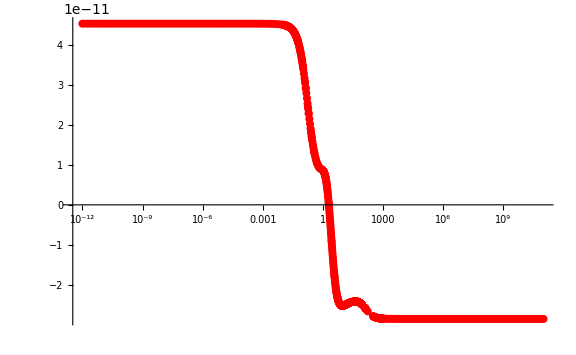

```mathematica
ListPlot[Table[{dlIM[[i,1]],Re[dlIM[[i,2]]]},{i,Length[dlIM]}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All,ScalingFunctions->{"Log",None},TicksStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```

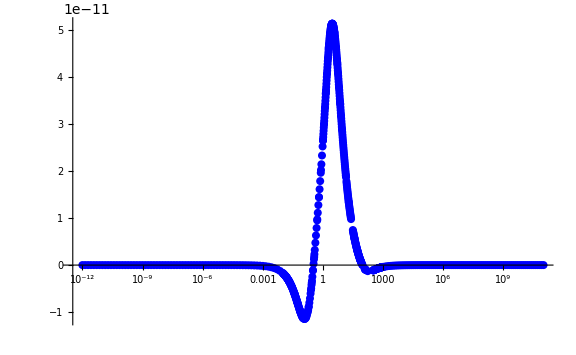

```mathematica
ListPlot[Table[{dlIM[[i,1]],Im[dlIM[[i,2]]]},{i,Length[dlIM]}],PlotStyle->{Blue,PointSize[0.01]},PlotRange->All,ScalingFunctions->{"Log",None},TicksStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```